```mathematica
Sigma[0] = SparseArray[IdentityMatrix[2]];
Sigma[1] = SparseArray[{{0, 1}, {1, 0}}];
Sigma[2] = SparseArray[{{0, -I}, {I, 0}}];
Sigma[3] = SparseArray[{{1, 0}, {0, -1}}];
Sigma[4]= (Sigma[1]+ I*Sigma[2])/2;
Sigma[5]= (Sigma[1]- I*Sigma[2])/2;
FullSigma[ a_, j_, nQubit_]:=SparseArray[KroneckerProduct[IdentityMatrix[2^(nQubit-j -1)], Sigma[a], IdentityMatrix[2^j]]]
```

```mathematica
HTFIM1D[J_, g_, N_]:= -J Sum[FullSigma[3, i,N]. FullSigma[3, Mod[i+1, N], N], {i, 0, N-1}]-g Sum[FullSigma[1, i, N], {i, 0, N-1}]
```

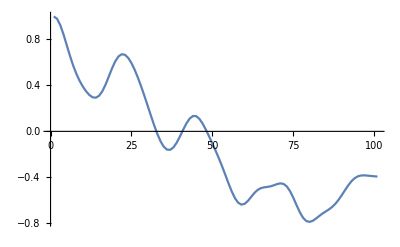

```mathematica
n=4;
Ham= HTFIM1D[1, 1, n];
initVec = Table[0, {i, 1, 2^n}];
initVec[[1]] = 1.0;
outStates = Table[MatrixExp[-I Ham t].initVec, {t, 0, 10, 0.1}];
ListPlot[Table[Conjugate[outStates[[i]]].FullSigma[3, 0, n].outStates[[i]], {i, 1, Length[outStates]}], Joined->True]
```

```mathematica
Table[Conjugate[outStates[[i]]].FullSigma[3, 0, n].outStates[[i]], {i, 1, Length[outStates]}]
```

{1.+0. ⅈ,0.980329+0. ⅈ,0.925086+0. ⅈ,0.844301+0. ⅈ,0.75102+0. ⅈ,0.657501+0. ⅈ,0.572354+0. ⅈ,0.499513+0. ⅈ,0.439038+0. ⅈ,0.389073+0. ⅈ,0.348039+0. ⅈ,0.316255+0. ⅈ,0.296459+0. ⅈ,0.293011+0. ⅈ,0.310017+0. ⅈ,0.349022+0. ⅈ,0.407251+0. ⅈ,0.477294+0. ⅈ,0.548544+0. ⅈ,0.609879+0. ⅈ,0.652444+0. ⅈ,0.67141+0. ⅈ,0.666148+0. ⅈ,0.639125+0. ⅈ,0.594279+0. ⅈ,0.535678+0. ⅈ,0.466805+0. ⅈ,0.39041+0. ⅈ,0.308693+0. ⅈ,0.223685+0. ⅈ,0.137766+0. ⅈ,0.0542013+0. ⅈ,-0.0225616+0. ⅈ,-0.0871375+0. ⅈ,-0.134077+0. ⅈ,-0.159102+0. ⅈ,-0.160218+0. ⅈ,-0.138318+0. ⅈ,-0.097192+0. ⅈ,-0.0431171+0. ⅈ,0.0157794+0. ⅈ,0.0704133+0. ⅈ,0.11202+0. ⅈ,0.133776+0. ⅈ,0.132336+0. ⅈ,0.108576+0. ⅈ,0.0670129+0. ⅈ,0.0139661+0. ⅈ,-0.0447907+0. ⅈ,-0.105825+0. ⅈ,-0.168529+0. ⅈ,-0.234191+0. ⅈ,-0.304221+0. ⅈ,-0.37836+0. ⅈ,-0.453594+0. ⅈ,-0.524143+0. ⅈ,-0.582588+0. ⅈ,-0.621872+0. ⅈ,-0.637628+0. ⅈ,-0.630039+0. ⅈ,-0.604339+0. ⅈ,-0.569493+0. ⅈ,-0.535327+0. ⅈ,-0.509216+0. ⅈ,-0.493826+0. ⅈ,-0.486922+0. ⅈ,-0.483336+0. ⅈ,-0.478079+0. ⅈ,-0.469124+0. ⅈ,-0.45867+0. ⅈ,-0.452459+0. ⅈ,-0.457592+0. ⅈ,-0.479735+0. ⅈ,-0.520715+0. ⅈ,-0.577299+0. ⅈ,-0.641584+0. ⅈ,-0.70301+0. ⅈ,-0.751419+0. ⅈ,-0.780135+0. ⅈ,-0.787843+0. ⅈ,-0.778448+0. ⅈ,-0.758996+0. ⅈ,-0.736606+0. ⅈ,-0.715824+0. ⅈ,-0.697496+0. ⅈ,-0.67938+0. ⅈ,-0.657912+0. ⅈ,-0.630144+0. ⅈ,-0.595074+0. ⅈ,-0.554058+0. ⅈ,-0.510446+0. ⅈ,-0.468671+0. ⅈ,-0.433077+0. ⅈ,-0.406751+0. ⅈ,-0.390692+0. ⅈ,-0.383673+0. ⅈ,-0.382904+0. ⅈ,-0.38522+0. ⅈ,-0.388238+0. ⅈ,-0.390923+0. ⅈ,-0.393417+0. ⅈ}

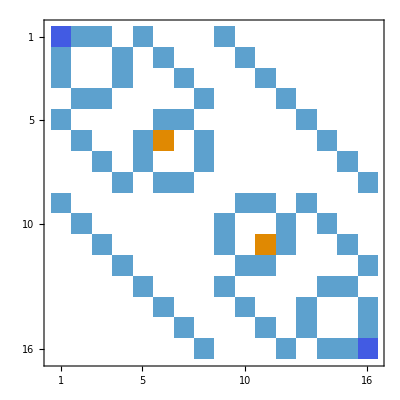

```mathematica
MatrixPlot[H]
```

```mathematica
MatrixForm[MatrixExp[-I  Pi KroneckerProduct[Sigma[3], Sigma[3]]]]
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
MatrixForm[CNOT. KroneckerProduct[Sigma[0], {{Exp[-I], 0}, {0, Exp[I]}}].CNOT]
```

(ⅇ^-ⅈ | 0 | 0 | 0
0 | ⅇ^ⅈ | 0 | 0
0 | 0 | ⅇ^ⅈ | 0
0 | 0 | 0 | ⅇ^-ⅈ)

```mathematica
MatrixForm[MatrixExp[-I H 10]]//N
```

(0.408082+0.912945 ⅈ | 0. | 0. | 0.
0. | 0.408082-0.912945 ⅈ | 0. | 0.
0. | 0. | 0.408082-0.912945 ⅈ | 0.
0. | 0. | 0. | 0.408082+0.912945 ⅈ)

```mathematica
TrotterRes001={{0,1},{0.5,0.653903},{1,0.343642},{1.5,0.340886},{2,0.647974},{2.5,0.541709},{3,0.148934},{3.5,-0.153805},{4,0.0117552},{4.5,0.11669},{5,-0.150961},{5.5,-0.49952},{6,-0.603969},{6.5,-0.491017},{7,-0.450468},{7.5,-0.611883},{8,-0.764011},{8.5,-0.683329},{9,-0.537222},{9.5,-0.38488},{10,-0.382844}}; 
TrotterRes01={{0,1},{0.5,0.540302},{1,0.231584},{1.5,0.147177},{2,0.430776},{2.5,0.625545},{3,0.384722},{3.5,0.0959599},{4,-0.0599436},{4.5,0.159041},{5,-0.00768846},{5.5,-0.0385198},{6,-0.18084},{6.5,-0.339039},{7,-0.348953},{7.5,-0.436582},{8,-0.360538},{8.5,-0.275028},{9,-0.423152},{9.5,-0.750365},{10,-0.747122}};
Clear[H]
```

```mathematica
ListPlot[{Table[{0.1 (i-1), Conjugate[outStates[[i]]].FullSigma[3, 0, n].outStates[[i]]}, {i, 1, Length[outStates]}], TrotterRes01, TrotterRes001}, Joined->{True, False, False}, PlotStyle->{Blue, Green, Red},PlotMarkers->{None, "x","x"},
PlotLegends->Placed[{"Exact", "Trotter Δt=0.5", "Trotter Δt=0.1"},{0.8,0.7}], AxesLabel->{"t", "<ψ(t)|Z_0 |ψ(t)>"}]
```

-Graphics-

```mathematica
,
```